# Model to describe the efficiency as a function of mass and ctau

```mathematica
f1[m_,E_,ct_,R_,z_]:=R/(2(E/m)ct(R^2+z^2))(Exp[(-√(R^2+z^2))/((E/m)ct)])  (* Exponencial decay of the GammaD *)
```

```mathematica
Zmax[m_,E_,ct_,R_]:= If[10.0 (E/m) ct<(10 R),10 (E/m) ct,10 R]
```

```mathematica
effR[R0_,R_]:= Which[R>0&&R<R0,1.0,R>R0,0.0] (* efficiency 1 before R0=9.8cm (3rd pixel layer) and zero above this value *)
```

```mathematica
Rmax[m_,E_,ct_]:=Which[10(E/m)ct<600,10(E/m)ct,10(E/m)ct≥600,600.0]
```

```mathematica
alpha0[m_]:=Which[m==0.25,0.0235,m==0.4,0.0198,m==0.7,0.019,m==1.0,0.0195,m==2.0,0.0189,m==5.0,0.0184,m==8.5,0.0184,m==15,0.0177,m==25,0.0219,m==35,0.0478,m==58,0.202] (*Efficiencies for ctau=0*)
```

```mathematica
datapoints= {{0.25,alpha0[0.25]},{0.4,0.06951},{0.7,alpha0[0.7]},{1.0,alpha0[1.0]},{2.0,alpha0[2.0]},{5.0,alpha0[5.0]},{8.5,alpha0[8.5]},{15.0,alpha0[15.0]},{25.0,alpha0[25.0]},{35.0,alpha0[35.0]},{58.0,alpha0[58.0]}};
```

```mathematica
feffR=Interpolation[datapoints,InterpolationOrder->1];
```

```mathematica
f3[m_,E_,ct_]:=NIntegrate[effR[160.0,R]2f1[m,E,ct,R,z],{R,0.0,Rmax[m,E,ct]},{z,0.0,Zmax[m,E,ct,R]}]
```

```mathematica
alphavsctau[m_,E_,ct_]:=feffR[m] f3[m,E,ct] f3[m,E,ct]  (* Final expression of the model with to variables m and ctau, the Energy for the GamamD = 50 GeV which is mean value of distribution *)
```

### Calling external data for limit setting (Br, limit on N, f(m), etc...)

```mathematica
(* Model Independent Limit *)
```

```mathematica
Nlimit = ReadList["/Users/alfredo/Documents/Github/DarkPhotonLimits_2022/2018_observed_limits.txt",{Real,Real}]; (* Br  GammaD to 2 mu *)
```

```mathematica
Nlimit;
```

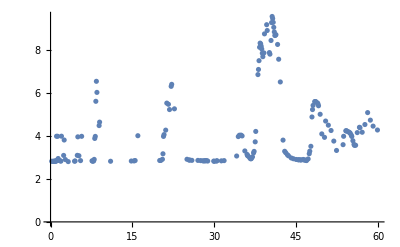

```mathematica
ListPlot[Nlimit]
```

```mathematica
Nlimitf = Interpolation[Nlimit,InterpolationOrder->1]
```

InterpolatingFunction[…]

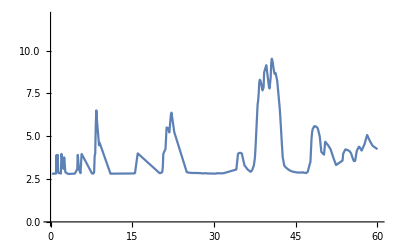

```mathematica
Plot[Nlimitf[m],{m,0.25,60.0},PlotRange->{{0.0,60.0},{0.0,12.0}}]
```

```mathematica
(*Nlimitf[x_]:=2.4+0.196258*Exp[-0.5*((x-0.585342)/0.0400199)^2]+1.32241*Exp[-0.5*((x-0.833146)/0.0350001)^2]+0.893637*Exp[-0.5*((x-1.16449)/0.033)^2]+1.79953*Exp[-0.5*((x-1.41323)/0.03)^2]+0.59907*Exp[-0.5*((x-1.90641)/0.05)^2]+1.1*Exp[-0.5*((x-2.40133)/0.042)^2]+2.20401*Exp[-0.5*((x-2.999)/0.169458)^2]+3.57*Exp[-0.5*((x-3.1005)/0.134076)^2]*)
(*Nlimitf[x_]:= 3.09*)
```

```mathematica
Br = ReadList["/Users/alfredo/Documents/Github/MuJetAnalysis_LimitsPlotting/scripts/Br_2018.dat",{Real,Real}]; (* Br  GammaD to 2 mu *)
```

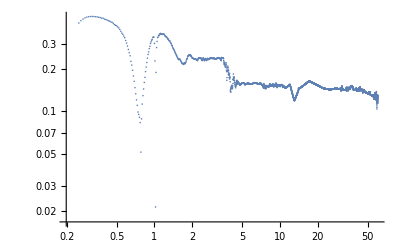

```mathematica
ListLogLogPlot[Br]
```

```mathematica
Brf = Interpolation[Br,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
listBrf = Table[{m,Brf[m]},{m,0.0,60.0,0.01}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

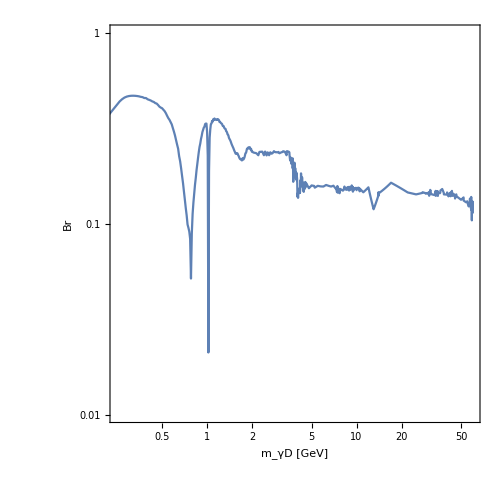

```mathematica
Brlog=ListLogLogPlot[listBrf,Joined->True,Joined->True,ImageSize->500,AspectRatio->1.0,TicksStyle->Directive[FontSize->16],Frame->True,FrameLabel->{"m_γD [GeV]","Br"},RotateLabel->True,BaseStyle->{FontSize->20},PlotRange->{{0.25,60.0},{0.01,1.0}}]
```

```mathematica
fm = ReadList["/Users/alfredo/Documents/Github/MuJetAnalysis_LimitsPlotting/scripts/fm_2018.dat",{Real,Real}]; (* Br  GammaD to 2 mu *)
```

```mathematica
fmf = Interpolation[fm,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
fmf[1.0]
```

124.279

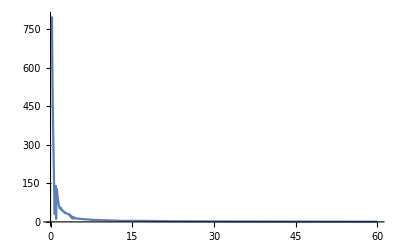

```mathematica
Plot[fmf[m],{m,0.25,60.0},PlotRange->{{0.0,60.0},{0.0,800}}]
```

#### Limit on Br(H→2γ) as a function of mass and ctau for different values (1%, 5%,10%,20%,40%)

```mathematica
(* Since we have epsilon as a function of the mass and ctau we cannot just plot the distributions as above, the limit is done in an iterative way getting the value in every mass bin and scanning in epsilon until it converges to the value of 3.07*)
```

```mathematica
ctauval[m_] := (1.97×10^-13 fmf[m])/10^Mineps2;  (* since our efficiency model is expresed in terms of ctau we need to correlate to which epsilon variable it correspond, at this step using epsilon^2 to avoid the sqrt *)
Nlimit2[m_,BrHtoGam_]:= 59.7 * 61000* BrHtoGam *  alphavsctau[m,50,ctauval[m]]* Brf[m] * Brf[m]; (*Higgs total cross seciton https://www.sciencedirect.com/science/article/pii/S037026931930228X *)(* This is the expression for the limit this expresion will be evaluated in the mass and ctau space until it converges to a value close to the limit on N(m) *)
```

```mathematica
Labelepsvsctau={"cτ=100.0","cτ=50.0","cτ=20.0","cτ=10.0","cτ=5.0","cτ=3.0","cτ=1.0","cτ=0.1","cτ=0.001","cτ=0.00001"}
```

{cτ=100.0,cτ=50.0,cτ=20.0,cτ=10.0,cτ=5.0,cτ=3.0,cτ=1.0,cτ=0.1,cτ=0.001,cτ=0.00001}

#### Br=0.1%

#### Br=1%

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.01; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,2.72};
step={0.1,0.1,0.1,0.1,0.1,0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.2 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,6,1}];
Export["/Users/alfredo/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_2023observed_m0to60_part1.dat",listbr1];
```

{{Null,Null}}

{1.04083×10^-17,0.25,-10.61,2.92745}

{0.06,0.35,-11.21,2.99808}

{0.03,0.45,-11.48,2.8818}

{0.05,0.55,-11.58,2.86041}

{0.05,0.65,-11.58,2.89084}

{0.06,0.7,-11.49,2.86454}

{0.04,0.8,-11.55,2.83878}

{0.09,0.85,-11.7,2.90459}

{0.07,0.95,-11.84,2.99876}

{1.04083×10^-17,1.,-11.89,2.90533}

{0.09,1.1,-11.9,4.03612}

{0.06,1.2,-12.05,2.9839}

{0.06,1.2,-12.05,2.9839}

{0.02,1.3,-12.03,4.12389}

{0.07,1.4,-12.16,3.06676}

{0.02,1.5,-12.21,3.04278}

{0.06,1.6,-12.26,3.02881}

{0.07,1.7,-12.32,2.84922}

{0.05,1.8,-12.36,3.03103}

{0.08,1.9,-12.42,2.95335}

{1.04083×10^-17,2.,-12.37,4.10864}

{1.04083×10^-17,2.,-12.37,4.10864}

{1.04083×10^-17,2.1,-12.43,3.82049}

{0.07,2.2,-12.48,3.64375}

{0.06,2.3,-12.54,3.42819}

{0.09,2.4,-12.6,3.09412}

{0.02,2.5,-12.57,3.91449}

{0.07,2.6,-12.64,3.44059}

{0.09,2.7,-12.7,3.13528}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.01; (* value of Br(H->GammaD) *)
min= {3.24}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={9.0};
step={0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.2 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfredo/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_2023observed_m0to60_part2.dat",listbr1];
```

{{Null,Null}}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.01; (* value of Br(H->GammaD) *)
min= {11.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={60};
step={0.5};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.2 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.02; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}]
Export["/Users/alfredo/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_2023observed_m0to60_part3.dat",listbr1]
```

{{Null,Null}}

{0.04,11.,-13.86,2.949}

{0.08,11.5,-13.9,2.96395}

{-6.93889×10^-18,12.,-13.94,2.98701}

{0.02,12.5,-13.96,2.85476}

{0.02,13.,-13.96,2.8691}

{0.08,13.5,-14.,2.98033}

{-6.93889×10^-18,14.,-14.06,2.90156}

{0.08,14.5,-14.1,2.88508}

{0.02,15.,-14.12,3.00286}

{0.06,15.5,-14.16,2.96868}

$Aborted

/Users/alfredo/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_1_2018data_2023observed_m0to60_part3.dat

#### Br=10%

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.1; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,2.72};
step={0.1,0.1,0.1,0.1,0.1,0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.2 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,6,1}];
Export["/Users/alfredo/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_2023observed_m0to60_part1.dat",listbr1];
```

{{Null,Null}}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.1; (* value of Br(H->GammaD) *)
min= {3.24}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={9.0};
step={0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.2 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfredo/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_2023observed_m0to60_part2.dat",listbr1];
```

{{Null,Null}}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.1; (* value of Br(H->GammaD) *)
min= {11.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={60};
step={0.5};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.2 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfredo/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_10_2018data_2023observed_m0to60_part3.dat",listbr1];
```

{{Null,Null}}

InterpolatingFunction::dmval: Input value {58.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

#### Br=30%

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.3; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,2.72};
step={0.1,0.1,0.1,0.1,0.1,0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.2 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,6,1}];
Export["/Users/alfredo/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_2023observed_m0to60_part1.dat",listbr1];
```

{{Null,Null}}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.3; (* value of Br(H->GammaD) *)
min= {3.24}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={9.0};
step={0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.2 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfredo/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_2023observed_m0to60_part2.dat",listbr1];
```

{{Null,Null}}

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.3; (* value of Br(H->GammaD) *)
min= {11.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={60};
step={0.5};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.1; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-18.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.2 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-18.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/alfredo/Documents/GitHub/DarkPhoton_Limits/Limit_epsvsmass_BrHtoGamD_30_2018data_2023observed_m0to60_part3.dat",listbr1];
```

{{Null,Null}}

InterpolatingFunction::dmval: Input value {58.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.